```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],Background->LightGray]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral2/D"]
```

/Users/spencerbryngelson/Desktop/Fortran/EV_spectral2/D

```mathematica
list=ReadList["x.000000001",Number];
real=Sort[Table[list[[i]],{i,1,Length[list],2}]];
imaginary=Sort[Table[list[[i]],{i,2,Length[list],2}]];
realsort=Sort[Abs[real]];
```

```mathematica
forevals=Sort[-real]
```

{-2.25×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.25×10^-8}

```mathematica
forevals2=Sort[imaginary]
```

{-15.2064,-15.1779,-10.8501,-9.68899,-7.8094,-6.2784,-4.71256,-3.1416,-1.5708,-4.43×10^-8,4.43×10^-8,1.5708,3.1416,4.71256,6.2784,7.8094,9.68899,10.8501,15.1779,15.2064}

```mathematica
ev1=Table[(i*Pi/2.),{i,0,(Length[forevals2]-1)/2}];
ev2=-ev1;
```

```mathematica
ExactEv=Sort[Join[ev1,ev2]]
```

{-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,0.,0.,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372}

```mathematica
error2=Sort[Abs[forevals2-ExactEv]]
```

{4.94897×10^-10,4.94897×10^-10,4.43×10^-8,4.43×10^-8,5.59291×10^-6,5.59291×10^-6,0.000167861,0.000167861,0.00478981,0.00478981,0.0445805,0.0445805,0.145499,0.145499,0.264212,0.264212,1.06927,1.06927,2.61156,2.61156}

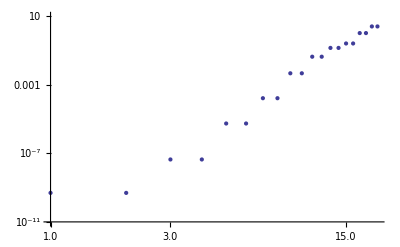

```mathematica
ListLogLogPlot[{error2},PlotRange->{10^-11,10}]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral2/V"];
```

```mathematica
data=Import[#,"Table"]&/@FileNames["x.*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
Table[realvec[i]=Table[vec[i][[j,1]],{j,1,Length[data]}],{i,1,Length[data]}];
Table[imvec[i]=Table[vec[i][[j,2]],{j,1,Length[data]}],{i,1,Length[data]}];
```

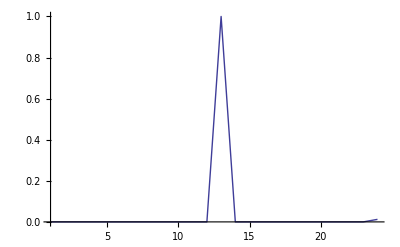
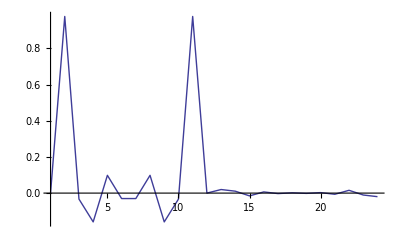
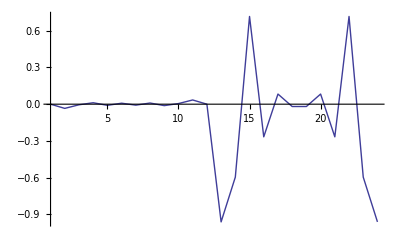
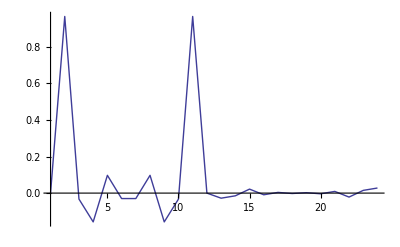
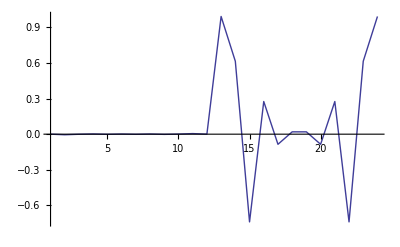
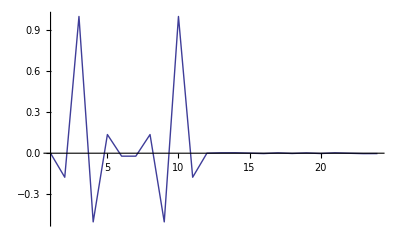
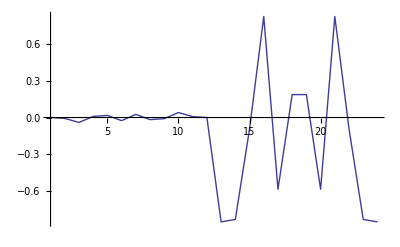
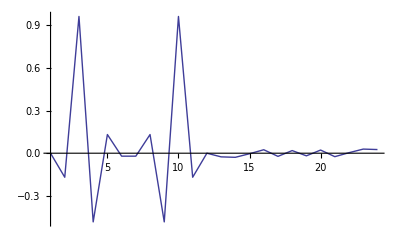

```mathematica
Table[ListPlot[realvec[i],PlotRange->All,Joined->True],{i,1,Length[data]}]
```

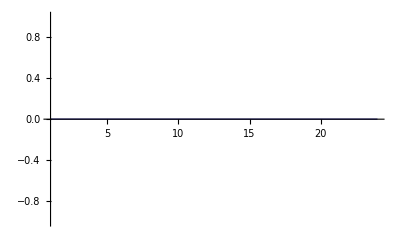
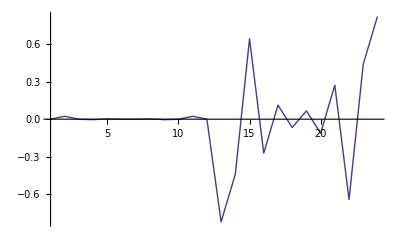
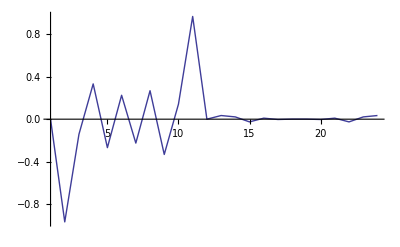
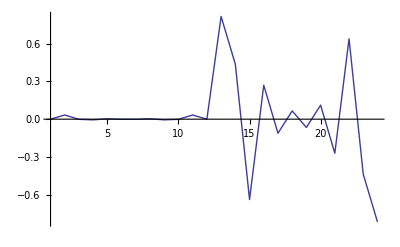
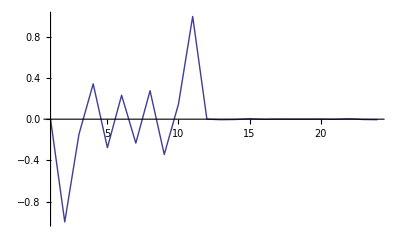
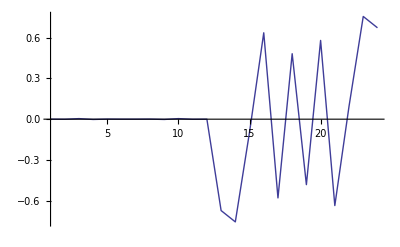
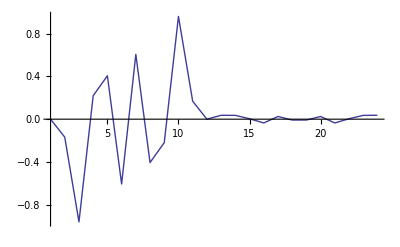
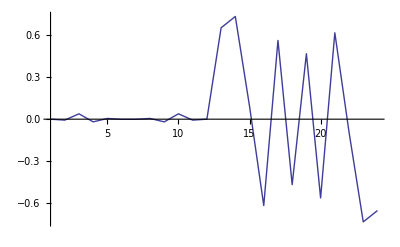
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[imvec[i],PlotRange->All,Joined->True],{i,1,Length[data]}]
```